```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\shiyi\DiFfRG\Examples\QuarkMesonLPAprime\build\datamub0

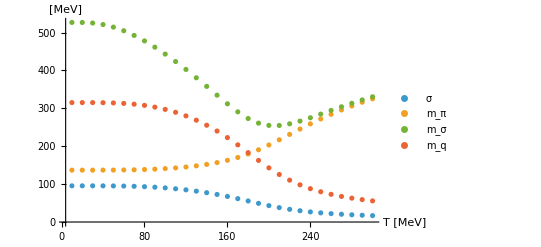

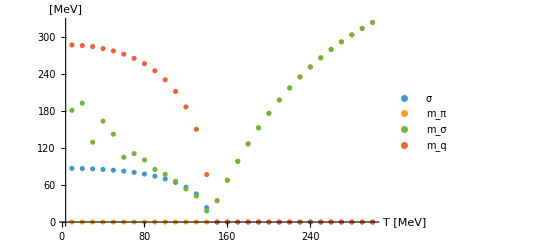

```mathematica
T=Table[i,{i,10,300,10}];
datasigma=Table[Transpose[Import["./T"<>ToString[NumberForm[i*0.01,{Infinity,2}]]<>"_data_running_EoM.csv"]][[3]][[-1]]*1000,{i,1,30}];
datamp=Table[Transpose[Import["./T"<>ToString[NumberForm[i*0.01,{Infinity,2}]]<>"_data_running_EoM.csv"]][[9]][[-1]]*1000,{i,1,30}];
datams=Table[Transpose[Import["./T"<>ToString[NumberForm[i*0.01,{Infinity,2}]]<>"_data_running_EoM.csv"]][[10]][[-1]]*1000,{i,1,30}];
datamq=Table[Transpose[Import["./T"<>ToString[NumberForm[i*0.01,{Infinity,2}]]<>"_data_running_EoM.csv"]][[11]][[-1]]*1000,{i,1,30}];
datasigmac=Table[Transpose[Import["./T"<>ToString[NumberForm[i*0.01,{Infinity,2}]]<>"_data_chiral.csv"]][[3]][[-1]]*1000,{i,1,30}];
datampc=Table[Transpose[Import["./T"<>ToString[NumberForm[i*0.01,{Infinity,2}]]<>"_data_chiral.csv"]][[9]][[-1]]*1000,{i,1,30}];
datamsc=Table[Transpose[Import["./T"<>ToString[NumberForm[i*0.01,{Infinity,2}]]<>"_data_chiral.csv"]][[10]][[-1]]*1000,{i,1,30}];
datamqc=Table[Transpose[Import["./T"<>ToString[NumberForm[i*0.01,{Infinity,2}]]<>"_data_chiral.csv"]][[11]][[-1]]*1000,{i,1,30}];
ListPlot[{Transpose[{T,datasigma}],Transpose[{T,datamp}],Transpose[{T,datams}],Transpose[{T,datamq}]},PlotLegends->{"σ","m_π","m_σ","m_q"},AxesLabel->{"T [MeV]","[MeV]"},PlotRange->All]
ListPlot[{Transpose[{T,datasigmac}],Transpose[{T,datampc}],Transpose[{T,datamsc}],Transpose[{T,datamqc}]},PlotLegends->{"σ","m_π","m_σ","m_q"},AxesLabel->{"T [MeV]","[MeV]"},PlotRange->All]
```

```mathematica
Import["./T10_data_running_EoM.csv"][[1]]
```

{t,kGeV,sigmaGeV,ZQ,ZPhi,etaQ,etaPhi,hPhi,m_piGeV,m_sigmaGeV,m_qGeV}

```mathematica
datak=Transpose[Import["./T0.01_data_running_EoM.csv"]][[2]][[2;;-1]]*1000;
datasigma=Transpose[Import["./T0.01_data_running_EoM.csv"]][[3]][[2;;-1]]*1000;
datampi=Transpose[Import["./T0.01_data_running_EoM.csv"]][[9]][[2;;-1]]*1000;
datams=Transpose[Import["./T0.01_data_running_EoM.csv"]][[10]][[2;;-1]]*1000;
datamq=Transpose[Import["./T0.01_data_running_EoM.csv"]][[11]][[2;;-1]]*1000;
datakc=Transpose[Import["./T0.01_data_chiral.csv"]][[2]][[2;;-1]]*1000;
datasigmac=Transpose[Import["./T0.01_data_chiral.csv"]][[3]][[2;;-1]]*1000;
datampic=Transpose[Import["./T0.01_data_chiral.csv"]][[9]][[2;;-1]]*1000;
datamsc=Transpose[Import["./T0.01_data_chiral.csv"]][[10]][[2;;-1]]*1000;
datamqc=Transpose[Import["./T0.01_data_chiral.csv"]][[11]][[2;;-1]]*1000;
datah=Transpose[Import["./T0.01_data_running_EoM.csv"]][[8]][[2;;-1]];
```

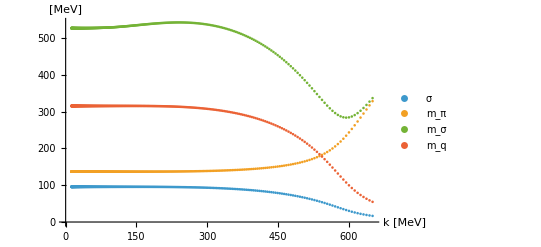

```mathematica
ListPlot[{Transpose[{datak,datasigma}],Transpose[{datak,datampi}],Transpose[{datak,datams}],Transpose[{datak,datamq}]},PlotRange->All,PlotLegends->{"σ","m_π","m_σ","m_q"},AxesLabel->{"k [MeV]","[MeV]"}]
```

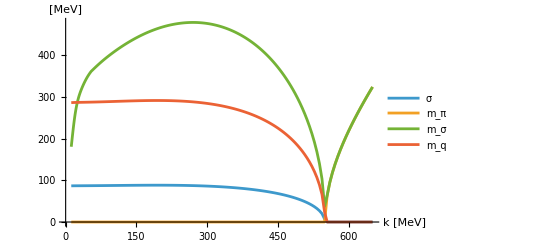

```mathematica
ListLinePlot[{Transpose[{datakc,datasigmac}],Transpose[{datakc,datampic}],Transpose[{datakc,datamsc}],Transpose[{datakc,datamqc}]},PlotRange->All,PlotLegends->{"σ","m_π","m_σ","m_q"},AxesLabel->{"k [MeV]","[MeV]"}]
```

```mathematica
datak=Transpose[Import["./T0.01_data_running_EoM.csv"]][[2]][[2;;-1]]*1000;
datasigma=Transpose[Import["./T0.01_data_running_EoM.csv"]][[3]][[2;;-1]]*1000;
datampi=Transpose[Import["./T0.01_data_running_EoM.csv"]][[9]][[2;;-1]]*1000;
datams=Transpose[Import["./T0.01_data_running_EoM.csv"]][[10]][[2;;-1]]*1000;
datamq=Transpose[Import["./T0.01_data_running_EoM.csv"]][[11]][[2;;-1]]*1000;
```

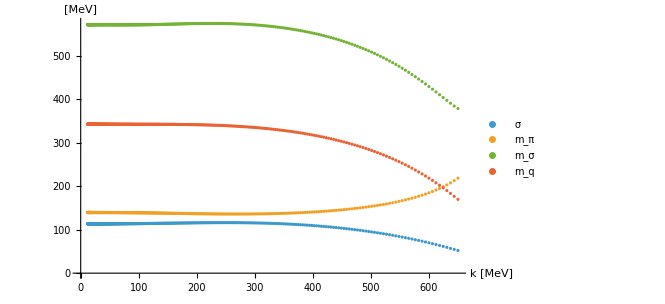

```mathematica
ListPlot[{Transpose[{datak,datasigma}],Transpose[{datak,datampi}],Transpose[{datak,datams}],Transpose[{datak,datamq}]},PlotRange->All,PlotLegends->{"σ","m_π","m_σ","m_q"},AxesLabel->{"k [MeV]","[MeV]"}]
```